## Analisi sistema LTI-TD

```mathematica
A = {{-17/36, -7/18, -7/18}, {17/72, 25/36, 43/36}, {-55/72, -11/36, 7/36}};
B = {{2/3}, {-1/3}, {-1/3}};
C1 = {{0, 1, -1}};
```

### Modi naturali del sistema

```mathematica
λ = Eigenvalues[A]
```

{1/2,-1/3,1/4}

```mathematica
T = Transpose[Eigenvectors[A]]
```

{{4,14/11,14/11},{-11,-16/11,-37/11},{1,1,1}}

```mathematica
T//MatrixForm
```

(4 | 14/11 | 14/11
-11 | -16/11 | -37/11
1 | 1 | 1)

```mathematica
Λ = Inverse[T].A.T
```

{{1/2,0,0},{0,-1/3,0},{0,0,1/4}}

```mathematica
Λ//MatrixForm
```

(1/2 | 0 | 0
0 | -1/3 | 0
0 | 0 | 1/4)

```mathematica
Simplify[MatrixPower[Λ,k]]//MatrixForm
```

(2^-k | 0 | 0
0 | (-1/3)^k | 0
0 | 0 | 4^-k)

```mathematica
λ[[1]]
```

1/2

Grafichiamo i modi naturali

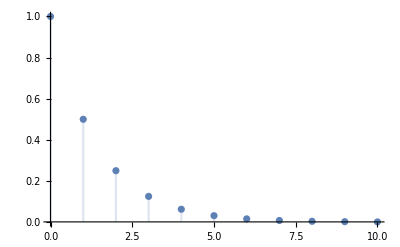

```mathematica
DiscretePlot[λ[[1]]^k, {k,0,10}, PlotRange->All]
```

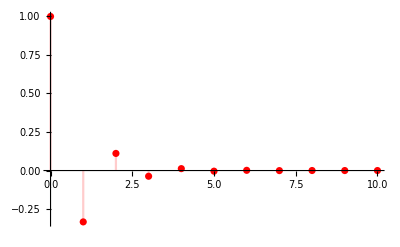

```mathematica
DiscretePlot[λ[[2]]^k, {k,0,10}, PlotRange->All,PlotStyle->Red]
```

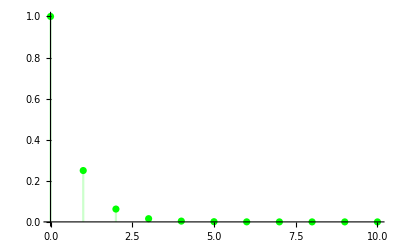

```mathematica
DiscretePlot[λ[[3]]^k, {k,0,10}, PlotRange->All, PlotStyle->Green]
```

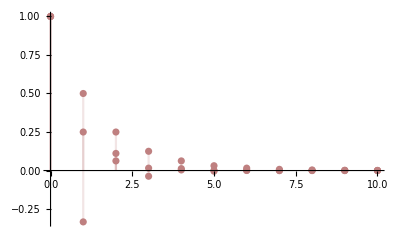

```mathematica
DiscretePlot[λ^k,{k,0,10},PlotRange->All, PlotStyle->RGBColor[0.75,0.5,0.5]]
```

### Risposta libera

```mathematica
Subscript[x, 09] = {{-3},{-1},{3}}
```

{{-3},{-1},{3}}

```mathematica
Subscript[x, 09]//MatrixForm
```

(-3
-1
3)

```mathematica
Subscript[z, 01]= Inverse[T].Subscript[x, 09]
```

{{-5/2},{-110/21},{451/42}}

```mathematica
Subscript[z, 01]//MatrixForm
```

(-5/2
-110/21
451/42)

```mathematica
{n,n} = Dimensions[A]
```

{3,3}

```mathematica
Subscript[x, l2][k_] := ∑_(i=1)^n T[[All, i]] λ[[i]]^k Subscript[z, 01][[i,1]]
```

```mathematica
Simplify[MatrixForm[Subscript[x, l2][k]]]
```

(1/3 (-20 (-1/3)^k-15 2^(1-k)+41 4^-k)
1/42 (320 (-1/3)^k+1155 2^-k-1517 4^-k)
1/42 (-220 (-1/3)^k-105 2^-k+451 4^-k))

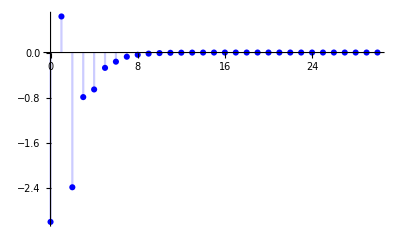

```mathematica
DiscretePlot[Subscript[x, l2][k][[1]], {k,0,30}, PlotRange->All, PlotStyle->Blue]
```

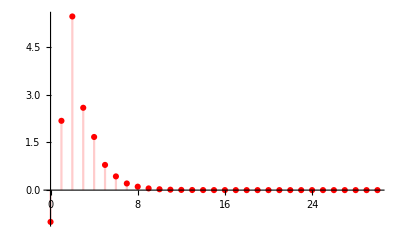

```mathematica
DiscretePlot[Subscript[x, l2][k][[2]], {k,0,30}, PlotRange->All, PlotStyle->Red]
```

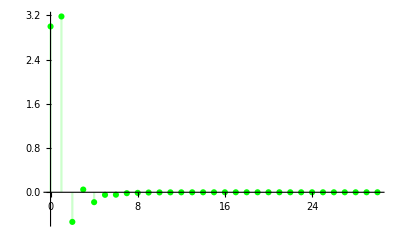

```mathematica
DiscretePlot[Subscript[x, l2][k][[3]], {k,0,30}, PlotRange->All, PlotStyle->Green]
```

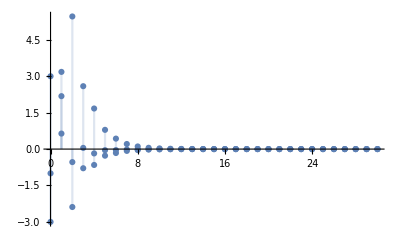

```mathematica
DiscretePlot[Subscript[x, l2][k],{k,0,30}, PlotRange->All]
```

### Configurazione iniziale

```mathematica
T//MatrixForm
```

(4 | 14/11 | 14/11
-11 | -16/11 | -37/11
1 | 1 | 1)

```mathematica
Subscript[x, 1] = 3 T[[All,1]]
```

{12,-33,3}

```mathematica
Subscript[z, 011]= Inverse[T].Subscript[x, 1]
```

{3,0,0}

```mathematica
Subscript[x, l1d][k_] := T.MatrixPower[Λ,k].Subscript[z, 011]
```

```mathematica
Subscript[x, l1d][k]
```

{3 2^(2-k),-33 2^-k,3 2^-k}

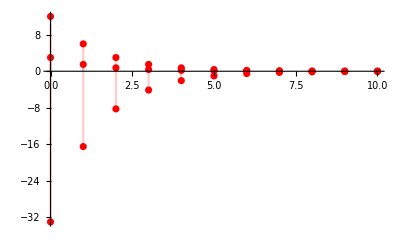

```mathematica
DiscretePlot[{Subscript[x, l1d][k]},{k,0,10},PlotRange->All,PlotStyle->Red]
```

```mathematica
Subscript[x, 2]= 3T[[All,2]]
```

{42/11,-48/11,3}

```mathematica
Subscript[z, 022]= Inverse[T].Subscript[x, 2]
```

{0,3,0}

```mathematica
Subscript[x, l2d][k_] := Expand[Simplify[T.MatrixPower[Λ,k]].Subscript[z, 022]]
```

```mathematica
Subscript[x, l2d][k]
```

{14/11 (-1)^k 3^(1-k),-16/11 (-1)^k 3^(1-k),(-1)^k 3^(1-k)}

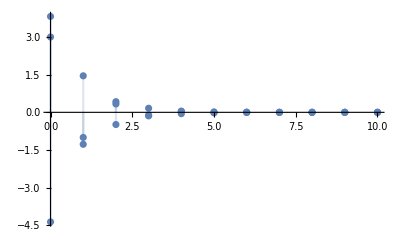

```mathematica
DiscretePlot[Subscript[x, l2d][k],{k,0,10},PlotRange->All]
```

```mathematica
Subscript[x, l2d2][k_] := Expand[Simplify[T.MatrixPower[A,k]].Subscript[x, 2]]
```

```mathematica
Subscript[x, l2d2][k]
```

{182/121 (-1)^k 3^(2-k),(10563 2^(-2 k))/121-205/121 (-1)^k 3^(3-k)-(1509 4^(2-k))/847-(4527 4^-k)/77,21/11 2^(2-2 k)+1/11 (-1)^k 3^(3-k)-(9 4^(1-k))/7-(3 4^(3-k))/77}

```mathematica
{14/11 (-1)^k 3^(1-k),(259 2^(-2 k))/11-16/11 (-1)^k 3^(1-k)-(37 4^(2-k))/77-(111 4^-k)/7,-7 2^(-2 k)+(-1)^k 3^(1-k)+4^(2-k)/7+(33 4^-k)/7}
```

{14/11 (-1)^k 3^(1-k),(259 2^(-2 k))/11-16/11 (-1)^k 3^(1-k)-(37 4^(2-k))/77-(111 4^-k)/7,-7 2^(-2 k)+(-1)^k 3^(1-k)+4^(2-k)/7+(33 4^-k)/7}

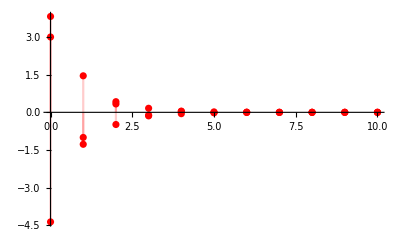

```mathematica
DiscretePlot[{Subscript[x, l2d][k]},{k,0,10},PlotRange->All,PlotStyle->Red]
```

```mathematica
Subscript[x, 3]=3T[[All,3]]
```

{42/11,-111/11,3}

```mathematica
Subscript[z, 3]= Inverse[T].Subscript[x, 3]
```

{0,0,3}

```mathematica
Subscript[x, l3d][k_]:=Expand[Simplify[MatrixPower[A,k]].Subscript[x, 3]]
```

```mathematica
Subscript[x, l3d2][k_]:= Expand[T.MatrixPower[Λ ,k].Subscript[z, 3]]
```

```mathematica
Subscript[x, l3d2][k]
```

{21/11 2^(1-2 k),-(111 4^-k)/11,3 4^-k}

```mathematica
Subscript[x, l3d2][k]/(1/4)^k
```

{42/11,-111/11,3}

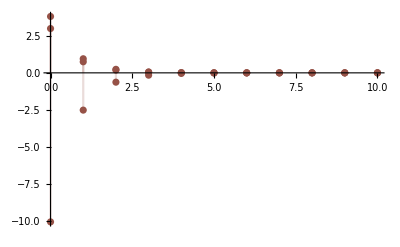

```mathematica
DiscretePlot[{Subscript[x, l3d2][k]},{k,0,10},PlotRange->All,PlotStyle->RGBColor[0.59,0.32,0.28]]
```

### Funzione di transizione

Passo ora al calcolo della funzione di stato

```mathematica
A = {{-17/36, -7/18, -7/18}, {17/72, 25/36, 43/36}, {-55/72, -11/36, 7/36}};
B = {{2/3}, {-1/3}, {-1/3}};
C1 = {{0, 1, -1}};
```

```mathematica
G[z_] := Simplify[(C1.Inverse[z IdentityMatrix[3] - A]).B]
```

```mathematica
G[z]
```

{{-24/(1-3 z-10 z^2+24 z^3)}}

Trovo gli zeri

```mathematica
Solve[Numerator[G[z][[1]] ]== 0,z]
```

{}

Trovo i poli

```mathematica
Solve[Denominator[G[z][[1]]]== 0, z]
```

{{z→-1/3},{z→1/4},{z→1/2}}

### Risposta al gradino

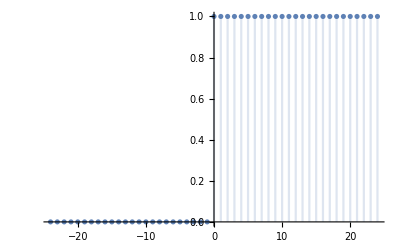

```mathematica
DiscretePlot[UnitStep[k], {k, -24,24}, PlotRange->All]
```

```mathematica
G[z]
```

{{-24/(1-3 z-10 z^2+24 z^3)}}

```mathematica
U[z] = z/(z - 1)
```

z/(-1+z)

```mathematica
Subscript[y, fd][z_] := G[z]U[z]
```

```mathematica
Subscript[y, fd][z]
```

{{-(24 z)/((-1+z) (1-3 z-10 z^2+24 z^3))}}

```mathematica
Apart[Subscript[y, fd][z]]
```

{{-2/(-1+z)+48/(5 (-1+2 z))-54/(35 (1+3 z))-64/(7 (-1+4 z))}}

Divido in fratti semplici e cerco i coefficienti
Il coefficiente della risposta a regime la posso trovare come G[1]

```mathematica
Subscript[y, rgm]= G[1][[1,1]]
```

-2

```mathematica
Subscript[C, 1] = Limit[(z-(1/2))(Subscript[y, fd][z]/z),z->(1/2) ][[1,1]]
```

48/5

```mathematica
Subscript[C, 2] = Limit[(z+(1/3))(Subscript[y, fd][z]/z),z->-(1/3) ][[1,1]]
```

54/35

```mathematica
Subscript[C, 3] = Limit[(z-(1/4))(Subscript[y, fd][z]/z),z->(1/4) ][[1,1]]
```

-64/7

```mathematica
Subscript[y, fzd] =Expand[InverseZTransform[Subscript[y, fd][z], z,k]]
```

-2-1/7 2^(6-2 k)+(3 2^(4-k))/5+2/35 (-1)^k 3^(3-k)

```mathematica
-2/35 (35+5 2^(5-2 k)-21 2^(3-k)-(-1)^k 3^(3-k))
```

-2/35 (35+5 2^(5-2 k)-21 2^(3-k)-(-1)^k 3^(3-k))

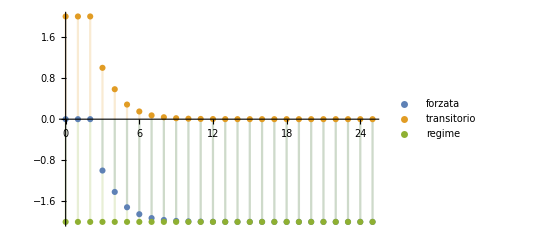

```mathematica
DiscretePlot[{Subscript[y, fzd],Subscript[y, fzd]-Subscript[y, rgm],Subscript[y, rgm]},{k,0,25},PlotRange->All, PlotLegends->{"forzata","transitorio", "regime"}]
```